```mathematica
(*Define the functions we'll need throughout the notebook*)
```

```mathematica
G[x_,μ_,σ_,A_]:= A/(√(2π σ^2))E^(-1/2((x-μ)/σ)^2);
H[x_,ω_] := 1/2 ω^2 x^2;
U[x_,ω_,A_,μ_,σ_]:= G[x,μ,σ,A] + H[x,ω];
F [x_,ω_,A_,μ_,σ_]:= -D[U[x,ω,A,μ,σ],{x,1}];
polyfun[N_,x_] := Sum[Subscript[r, n] x^(n-1),{n,1,N+1}];DampedSine[t_,a_,b_,c_,d_,e_]:= a E^(-b t)Sin[ c t + d]+e;
```

```mathematica
(* Parameters defined externally because lazy/stupid*)zerofit[A_]:=(soln=NDSolve[{x''[t] == F [x[t],ω,A,μ,σ]-β x'[t],x[0]==0,x'[0]==v0},x,{t,0,30}];fsamp=10*ω;tmax=20;dt=1/fsamp;nsamp=fsamp*tmax;
T = Table[n*dt,{n,0,nsamp}];X =x[t]/.t->T/.soln[[1]];DSdata=Table[{T[[i]],X[[i]]},{i,1,Length[T]}];nlm = NonlinearModelFit[DSdata,DampedSine[t,a,b,c,d,e] ,{a,b,c,d,e},t];nlm[[1]][[2]]);
```

```mathematica
(*Setting parameters*)
fsamp=10*ω;tmax=25;dt=1/fsamp;nsamp=fsamp*tmax;
(*Doing the work*)
Manipulate[soln=NDSolve[{x''[t] == F [x[t],ω,A,μ,σ]-β x'[t],x[0]==0,x'[0]==3},x,{t,0,tmax}];
xrange=2;sz=300;T = Table[n*dt,{n,0,nsamp}];X =x[t]/.t->T/.soln[[1]];DSdata=Table[{T[[i]],X[[i]]},{i,1,Length[T]}];nlm = NonlinearModelFit[DSdata,DampedSine[t,a,b,c,d,e] ,{a,b,c,d,e},t];delta[t_]:=Evaluate[x[t]/.soln]-nlm[t];
f0 =  Plot[G[x,μ,σ,A] ,{x,-xrange,xrange},PlotRange->{-25,25},PlotStyle->{Orange,Opacity[0.5]},PlotLabel->"Potential",PlotLegends->{"Probe"},AxesLabel->{"x","U(x)"}];
f00=Plot[H[x,ω] ,{x,-xrange,xrange},PlotStyle->{Red,Opacity[0.5]},PlotLegends->{"Trap"}];
f1=Plot[Evaluate[G[x,μ,σ,A] + H[x,ω]], {x,-xrange,xrange},PlotStyle->Black,PlotLegends->{"Net"},AxesLabel->{"x","F(x)"}];
f2=Plot[Evaluate[D[G[x,μ,σ,A] + H[x,ω],{x,1}]], {x,-xrange,xrange},PlotRange->Full,PlotLabel->"Force"];
f31=Plot[Evaluate[x[t]/.soln],{t,0,tmax},PlotRange->Full,PlotLabel->"Motion",AxesLabel->{"t","x(t)"}];f32=Plot[nlm[t],{t,0,tmax},PlotStyle->Red];f4=Plot[delta[t],{t,0,tmax},PlotLabel->"Residuals",AxesLabel->{"t,","Δx(t)"}];verbout = "Text";Grid[{{Show[f0,f00,f1,ImageSize->sz],Show[f2,ImageSize->sz]},{Show[f31,f32,ImageSize->sz],Show[f4,ImageSize->sz],Text[c/.nlm[[1]][[2]]]}}],{{ω,5,"Frequency"},1,6},{{μ,-0.3,"Beam centre"},-3,3},{{σ,1,"Beam waist"},0.1,2},{{A,-50,"Amplitude"},-100,100},{{β,0.18,"Damping"},0,3},ContentSize->{800, 460}]
```

Table::iterb: Iterator {n,0,250 ω} does not have appropriate bounds.

Part::partw: Part 2 of «1»[Table[n dt,{n,0,250 ω}]] does not exist.

Table::iterb: Iterator {n,0.,250. ω} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partw: Part 2 of «1»[Table[n dt,{n,0.,250. ω}]] does not exist.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

Part::partw: Part 2 of «1»[Table[n dt,{n,0.,250. ω}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

General::ivar: 0.000510714 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::rmix: Elements of {{n,0,250 ω},«1»} are a mixture of lists and nonlists.

Table::iterb: Iterator {n,0,250 ω} does not have appropriate bounds.

Part::partw: Part 2 of «1»[Table[n dt,{n,0,250 ω}]] does not exist.

Table::iterb: Iterator {n,0.,250. ω} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partw: Part 2 of «1»[Table[n dt,{n,0.,250. ω}]] does not exist.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

Part::partw: Part 2 of «1»[Table[n dt,{n,0.,250. ω}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

General::ivar: 0.000510714 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::rmix: Elements of {{n,0,250 ω},«1»} are a mixture of lists and nonlists.

Table::iterb: Iterator {n,0,250 ω} does not have appropriate bounds.

Part::partw: Part 2 of «1»[Table[n dt,{n,0,250 ω}]] does not exist.

Table::iterb: Iterator {n,0.,250. ω} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partw: Part 2 of «1»[Table[n dt,{n,0.,250. ω}]] does not exist.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

Part::partw: Part 2 of «1»[Table[n dt,{n,0.,250. ω}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

General::ivar: 0.000510714 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::rmix: Elements of {{n,0,250 ω},«1»} are a mixture of lists and nonlists.

Table::iterb: Iterator {n,0,250 ω} does not have appropriate bounds.

Part::partw: Part 2 of «1»[Table[n dt,{n,0,250 ω}]] does not exist.

Table::iterb: Iterator {n,0.,250. ω} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partw: Part 2 of «1»[Table[n dt,{n,0.,250. ω}]] does not exist.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

Part::partw: Part 2 of «1»[Table[n dt,{n,0.,250. ω}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

General::ivar: 0.000510714 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

ReplaceAll::rmix: Elements of {{n,0,250 ω},«1»} are a mixture of lists and nonlists.

Table::iterb: Iterator {n,0,250 ω} does not have appropriate bounds.

Part::partw: Part 2 of «1»[Table[n dt,{n,0,250 ω}]] does not exist.

Table::iterb: Iterator {n,0.,250. ω} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partw: Part 2 of «1»[Table[n dt,{n,0.,250. ω}]] does not exist.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

Part::partw: Part 2 of «1»[Table[n dt,{n,0.,250. ω}]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument {{n/(10 ω),Table[n dt,{n,0,250 ω}]},«1»} in NonlinearModelFit is not a list or a rectangular array.

General::ivar: 0.000510714 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

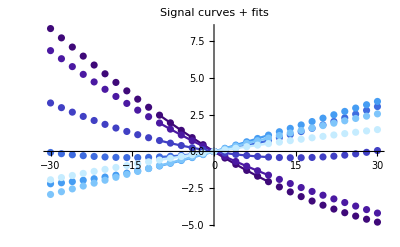
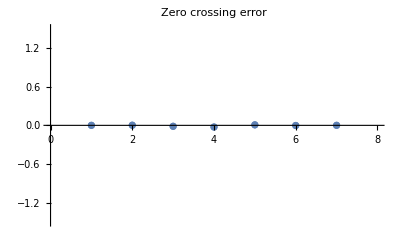

```mathematica
(* Parameters*)
{μmin,μmax,μstep,σ,ω,β,v0,polynomialorder} = {0,3,0.5,1,4,0,5,5};
(*Heavy lifting*)
Quiet[pfun = polyfun[polynomialorder,x];Errs = Table[Avals = Range[-30,30,2];
args =Tuples[{muvals,Avals}];
err=c^2-ω^2/.zerofit/@Avals;Transpose[{Avals,err}],{μ0,μmin,μmax,μstep}];ptable=Table[s=FindFit[Errs[[idx,All,All]],pfun ,CoefficientList[pfun,x],x];zero=FindRoot[pfun/.s,{x,0}];{plt0=ListPlot[Errs[[idx,All,All]],PlotStyle->ColorData["DeepSeaColors"][idx/Length[Errs]]],plt1=Plot[pfun/.s,{x,-10,10},PlotStyle->ColorData["DeepSeaColors"][idx/Length[Errs]]],plt2=ListPlot[{{idx,x/.zero}}]},{idx,1,Length[Errs]}];{Show[ptable[[All,1;;2]],ImageSize->400,PlotLabel->"Signal curves + fits"],Show[ptable[[All,3]],ImageSize->400,PlotLabel->"Zero crossing error",PlotRange->{{0,8},{-1.5,1.5}}]}]
```